## Harper’s Wolfram Language Cheat Sheet

```mathematica
(*What's the deal with all the @s?*)
```

```mathematica
ToUpperCase@{"a","b","c"} (*@ is just like regular brackets*)
```

{A,B,C}

```mathematica
ToUpperCase@@{"a"}
```

A

```mathematica
Plus@@{1,2,3} (*replaces curly brackets with normal brackets*)
```

6

```mathematica
Plus@@@{{1,2},{3,4}}
```

{3,7}

```mathematica
Plus@@@{1,2,3}
```

{1,2,3}

```mathematica
Plus@{{1,2},{3,4}}
```

{{1,2},{3,4}}

```mathematica
ToUpperCase/@{"a","b","c"} (*/@ applies to every element in a list*)
```

{A,B,C}

```mathematica
(*Lists and such*)
```

```mathematica
{1,1,2}*{1,2,3}
```

{1,2,6}

```mathematica
Count[{a,b,a,a,c,b,a},a]
```

4

```mathematica
Transpose[{{1,2},{3,4}}]
```

{{1,3},{2,4}}

```mathematica
Transpose[{{4,5,6,7,8},{9,10,11,12,13}}]
```

{{4,9},{5,10},{6,11},{7,12},{8,13}}

```mathematica
Part[{1,2,3,4,5},5]
```

5

```mathematica
{1,2,3,4,5}[[5]]
```

5

```mathematica
{1,2,3,4,5}[[3;;5]]
```

{3,4,5}

```mathematica
(*associations*)
```

```mathematica
<|1->a,2->b,3->c|>
```

```mathematica
<|1->a,2->b,3->c|>[[2]]
```

b

```mathematica
Sort[<|1->a,2->b,4->d,3->c|>]
```

<|1→a,2→b,3→c,4→d|>

```mathematica
KeySort[<|1->a,2->b,4->d,3->c|>]
```

<|1→a,2→b,3→c,4→d|>

```mathematica
(*association with a pure function*)
```

```mathematica
f[#apples,#oranges]&[<|"apples"->10,"oranges"->12,"pears"->4|>]
```

f[10,12]

```mathematica
(*arrays*)
```

```mathematica
(*an array is a table with two axes*)
```

```mathematica
Grid[Table[i,{i,4},{j,5}]]
```

1 | 1 | 1 | 1 | 1
2 | 2 | 2 | 2 | 2
3 | 3 | 3 | 3 | 3
4 | 4 | 4 | 4 | 4

```mathematica
(*dealing with real-world data*)
```


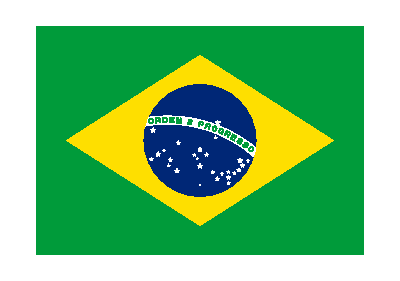


```mathematica
EntityValue[{Entity["Country","UnitedStates"],Entity["Country","Brazil"],Entity["Country","China"]},"Flag"]
```

```mathematica
EntityValue[""]
```

```mathematica
(*the above can tell any number of things*)
```

```mathematica
(*graphics tools*)
```

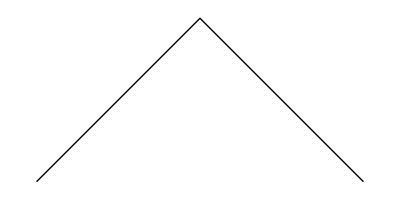

```mathematica
Graphics[Line[{{1,2},{3,4},{5,2}}]]
```

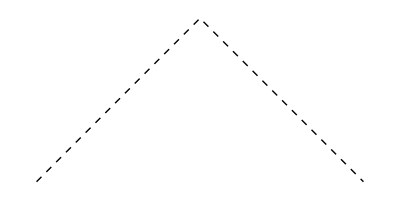

```mathematica
Graphics[{Dashed,Line[{{1,2},{3,4},{5,2}}]}]
```

```mathematica
(*Modules*)
```

```mathematica
Module[{x=3},x^2]
```

9

```mathematica
Module[{x=Range[10],y=2},x y]
```

{2,4,6,8,10,12,14,16,18,20}

```mathematica
(*multiplication by justaposition*)
```

```mathematica
(*this works:*)
```

```mathematica
Module[{x=Range[10],y=2},x y]
```

{2,4,6,8,10,12,14,16,18,20}

```mathematica
(*but this does not*)
```

```mathematica
Module[{x=Range[10],y=2},xy]
```

xy

```mathematica
(*patterns*)
```

```mathematica
MatchQ[{a,x,b},{_,x,_}]
```

True

```mathematica
Cases[{{a,a},{b,a},{a,b,c},{b,b},{c,a},{b,b,b}},{_,_}]
```

{{a,a},{b,a},{b,b},{c,a}}

```mathematica
EvenQ[3]
```

False

```mathematica
MatchQ[3,3]
```

True

```mathematica
MatchQ[{3,3},{_,_}]
```

True

```mathematica
(*If statements*)
```

```mathematica
Clear[x]
```

```mathematica
Module[{x=RandomInteger[]},If[OddQ[x],3,4]]
```

3